## Import data files and create interpolation objects

Native Coulomb wave form factors span the range E = 1 eV to 109.648 eV and:
outer valence Zeff=1:
for 6a, q = 1 to 38.89 keV.
q is the momentum transfer [in keV] and E is the electron kinetic energy [in keV].

The outgoing electron is centred on is centred on the position (0, 0, 2.78357) Bohr in our Cartesian coordinate system, which is the position of one of the hydrogen atoms.

For higher values of q than those above (where the form factor is very very small), we also give form factors where we match onto the (rescaled) plane wave results. The plots at the bottom of the notebook show this extrapolation.

### Coulomb wave

```mathematica
(*outer valence Zeff=1*)
SetDirectory[NotebookDirectory[]];
LC4H106a1grid=Import["C4H10_CW_6a_grid.dat"];
ResetDirectory[];

fC4H106a1=Interpolation[LC4H106a1grid,InterpolationOrder->1]
```

InterpolatingFunction[…]

### Coulomb wave + matched rescaled Plane wave at high q

```mathematica
(*outer valence Zeff=1*)
SetDirectory[NotebookDirectory[]];
LC4H10CWPW6a1grid=Import["C4H10_6a_grid_PW_largeQ.dat"];
ResetDirectory[];

fC4H10CWPW6a1=Interpolation[LC4H10CWPW6a1grid,InterpolationOrder->1]
```

InterpolatingFunction[…]

### Plots

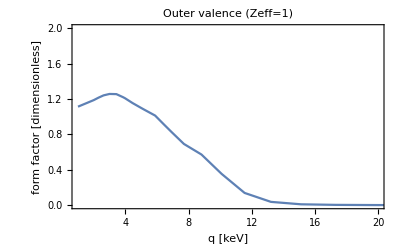

```mathematica
EtestkeV=0.025;

Plot[{fC4H106a1[q,EtestkeV]},{q,1,50},PlotRange->{{1,20},{0,2}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotLabel->"Outer valence (Zeff=1)"]
```

### Plots - showing the plane wave extrapolation in black

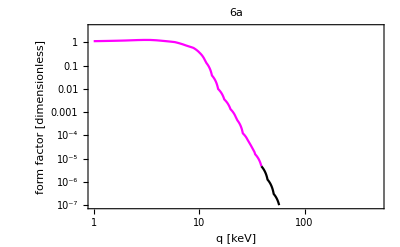

```mathematica
EtestkeV=0.025;

Show[LogLogPlot[{fC4H106a1[q,EtestkeV]},{q,1,LC4H106a1grid[[-1,1]]},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->Magenta],LogLogPlot[{fC4H10CWPW6a1[q,EtestkeV]},{q,LC4H106a1grid[[-1,1]],200},PlotRange->{{1,500},{10^-7,4}},Frame->True,FrameLabel->{"q [keV]","form factor [dimensionless]"},PlotStyle->{Black}],PlotLabel->"6a"]
```